-Graphics-

Narcissistic Numbers

Students

Baskaya, Semi Kaan, Student-ID, s_baskaya23@stud.hwr-berlin.de

Busson, Jan, Student-ID, s_busson23@stud.hwr-berlin.de

Haaken, Jan, Student-ID, xxx.xxx@xxx.de

Lecture		Optimization and Data Analytics

Lecturer		Prof. Dr. Frank Brand

## Content Overview

Statutory Declaration

1 Executive Summary     xx

2 Intoduction     xx

3 Problem Statement     xx

4 Solution     xx

4.1 xxx     xx

4.2 xxx     xx

4.3 xxx     xx

5 Sensitivity Analysis     xx

5.1 xxx     xx

5.2 xxx     xx

5.3 xxx     xx

6 Possible Generalizations of the Problem     xx

6.1 xxx     xx

6.2 xxx     xx

6.3 xxx     xx

7 Consequenses and Recommendations     xx

8 Summary of results     xx

## Statutory Declaration

I hereby formally declare that we have written the submitted term peper entirely by ourselfes without anyone else’s assistance. Wherever we have drawn on literature or other sources, either in direct quotes or in paraphrasing such material, we have given the reference to the original author or authors and to the source where it appeared. We are aware that the use of quotations, or close paraphrasing, from books, magazines, newspapers, the internet, or other sources, which are not marked as such, will be considered an attempt at deception, and that the term paper will be graded with a fail. We are aware of the fact, that the use of Large Language Models (LLM) like ChatGPT or others without a quotation will be graded with a fail, too.

____________________

Location / Date

___________________________

Signature

___________________________

Signature

___________________________

Signature

## 1 Executive Summary

Narcissistic numbers (or Armstrong number) are numbers that can be recreated by summing each of their digits raised to the power of the total number of digits in the number itself. For example, the number 153 is a narcissistic number because it has three digits and satisfies the equation:

153 = 1^3+5^3+3^3

The objective of this project is to find as many narcissistic numbers as possible. A major challenge is the rapidly increasing runtime required to test larger numbers. A pure brute force approach checks every number individually by calculating the sum of its powered digits and comparing the result with the original number. However, the search space grows exponentially with the number of digits.

For example if checking a single number requires only 1 microsecond (10^-6 seconds) testing all numbers up to:
(10^6) numbers would already take about 1 second, (10^9) numbers would take about 17 minutes, (10^12) numbers would require around 11.5 days, and (10^15) numbers would take more than 31 years.

Because of this exponential growth, the main task of this project is to develop an optimized algorithm and strategies that minimize runtime as much as possible. The more efficient the approach is, the more narcissistic numbers can realistically be found within a limited amount of computeation time.

## 2 Intoduction

This Mathematica notebook documents the project “Narcissistic Numbers”. The project was completed as part of the course Optimization and Simulation during the Summer Semester 2026.

## 3 Problem Statement

Narcissistic numbers, also known as Armstrong numbers, are a special subset of natural numbers. An n digit number, where n means its dimension, is defined as narcissistic if the sum of its digits, each raised to the power of n, is equal to the number itself.

A well known example of a three digit narcissistic number (n = 3) is: 153 = 1^3+5^3+3^3 (Note: 153 = 1 + 125 + 27)

In 1985, D. Winter mathematically proved that within the base 10 numeral system, narcissistic numbers can only exist up to a maximum length of 60 digits. This upper bound is derived from the following inequality constraint [1]: n*9^n < 10^(n-1)

For any dimension greater than 60, the maximum possible sum of the powered digits (n*9^n) is strictly less than the smallest possible number of that length (10^(n-1)), making the existence of larger narcissistic numbers mathematically impossible. Consequently, there are exactly 88 narcissistic numbers in base 10, with the largest being the 39 digit number:

115,132,219,018,763,992,565,095,597,973,971,522,401

The primary objective of this term paper is to develop and implement the most efficient algorithmic approach to search for and identify as many of these 88 narcissistic numbers as computationally feasible.

## 4 Solution

The following parameters define the dimension up to which an approach runs. They can be configured to test and compare the performance and speed of the different approaches presented in this notebook.

```mathematica
maxdimension = 6;
```

The first step is to define a function that can check whether any given number is narcissistic. For this purpose, a quality function QF is defined.

```mathematica
F[n_]:=Sum[IntegerDigits[n][[i]]^IntegerLength[n],{i,1,IntegerLength[n]}]
```

The quality function is derived by subtracting the digit power sum of a number from the number itself. Squaring this ensures that the function yields only positive values. Now narcissistic numbers represent not only the roots (zero) but also the global minima of the quality function.

In optimization theory, this squared approach acts like a quadratic penalty function. The squaring mechanism penalizes larger deviations from the target value.

```mathematica
QF[n_]:=(n-Sum[IntegerDigits[n][[i]]^IntegerLength[n],{i,1,IntegerLength[n]}])^2
```

For all narcissistic numbers: QF(n) = 0

```mathematica
QF[153]
```

0

For all non narcissistic numbers: QF(n) ≠ 0

```mathematica
QF[152]
```

324

The figure shows the values of the quality function QF(n) for integers 0 ≤ n ≤ 25.The zeros of the graph identify all narcissistic numbers in the considered range. Since every single digit number is equal to the sum of its digits raised to the first power, the numbers 0-9 appear as zeros of the function. Values close to zero indicate numbers that nearly satisfy the narcissistic condition.

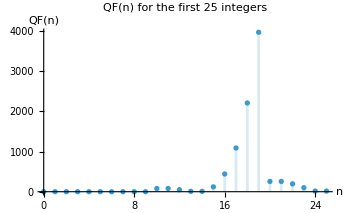

```mathematica
Show[DiscretePlot[QF[n],{n,0,25},AxesLabel->{"n","QF(n)"},PlotLabel->"QF(n) for the first 25 integers"],PlotRange->Full]
```

The following function returns all narcissistic numbers in the interval from 0 up to a given number n. In addition, it returns the time required for the calculation.

```mathematica
returnNarcissistic[n_]:=Module[{time,numbers},{time,numbers}=AbsoluteTiming[Select[Range[0,n],QF[#]==0&]];
{numbers,time}]
```

### 4.1 Bruteforce

Brute force describes an algorithmic approach in which all possible candidates are tested until a solution is found. Since this method does not use any filtering or optimization strategies, it is computationally more expensive than more advanced algorithms.

In this case, the brute force approach checks every number within the given range. For each number, the quality function is evaluated in order to determine whether the number is narcissistic or not.

Source: https://dl.acm.org/doi/10.1145/3107239, accessed June 16, 2026.

The following table shows all narcissistic numbers found up to each power of 10, as well as the corresponding computation time.

```mathematica
rows=Table[Module[{numbers,time},{numbers,time}=returnNarcissistic[10^k];
{Superscript[10,k],Row[numbers,"; "],NumberForm[time,{Infinity,3}]}],{k,0,maxdimension}];

Grid[Prepend[rows,{"Upper Bound","Numbers","Time in seconds"}],Frame->All]
```

Upper Bound | Numbers | Time in seconds
10^0 | ; ; 01 | 0.000
10^1 | ; ; 0123456789 | 0.000
10^2 | ; ; 0123456789 | 0.002
10^3 | ; ; 0123456789153370371407 | 0.024
10^4 | ; ; 0123456789153370371407163482089474 | 0.224
10^5 | ; ; 0123456789153370371407163482089474547489272793084 | 2.747
10^6 | ; ; 0123456789153370371407163482089474547489272793084548834 | 30.281

The table shows that the brute force approach becomes inefficient as the search range increases, because every number in the range is checked individually. Nevertheless, it remains useful as a simple baseline for validating later approaches. However, it is not suitable as a final solution for this problem, so a more optimized approach is required.

### 4.2 Bruteforce parallelized

The brute force approach can be improved by parallelizing the evaluation of the candidate numbers. Since the quality function can be applied to each number independently, the search range is distributed across multiple Mathematica subkernels using ParallelTable. Each candidate number is tested by evaluating QF[n], and numbers with QF[n] = 0 are identified as narcissistic numbers.

Although this reduces the computation time, the algorithm still checks every number in the given range. Therefore, the parallelized brute force approach improves practical runtime but does not solve the scalability problem of the original brute force method.

```mathematica
LaunchKernels[];

DistributeDefinitions[F,QF];

returnNarcissisticParallel[n_]:=Module[{time,numbers},{time,numbers}=AbsoluteTiming[ParallelTable[If[QF[i]==0,i,Nothing],{i,0,n},Method->"CoarsestGrained"]];
{numbers,time}]
```

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

```mathematica
maxdimension=7;

rows=Table[{numbers,time}=returnNarcissisticParallel[10^k];
{Superscript[10,k],Row[numbers,"; "],NumberForm[time,{Infinity,3}]},{k,0,maxdimension}];

Grid[Prepend[rows,{"Upper Bound","Numbers","Time in seconds"}],Frame->All]
```

Upper Bound | Numbers | Time in seconds
10^0 | ; ; 01 | 0.051
10^1 | ; ; 0123456789 | 0.073
10^2 | ; ; 0123456789 | 0.010
10^3 | ; ; 0123456789153370371407 | 0.035
10^4 | ; ; 0123456789153370371407163482089474 | 0.092
10^5 | ; ; 0123456789153370371407163482089474547489272793084 | 0.597
10^6 | ; ; 0123456789153370371407163482089474547489272793084548834 | 6.393
10^7 | ; ; 01234567891533703714071634820894745474892727930845488341741725421081898008179926315 | 70.916

### 4.3 XXX

--- Text here ---

## 5 Sensitivity Analysis

### 5.1 XXX

--- Text here ---

### 5.2 XXX

--- Text here ---

### 5.3 XXX

--- Text here ---

## 6 Possible Generalizations of the Problem

### 6.1 XXX

--- Text here ---

### 6.2 XXX

--- Text here ---

### 6.3 XXX

--- Text here ---

## 7 Consequenses and Recommendations

--- Text here ---

## 8 Summary of results

--- Text here ---